Possible Games with n Players - Log Plot:

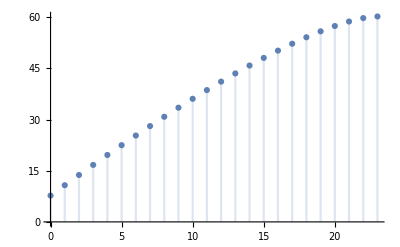

{n = 0 ->,5.2×10^7}
{n = 1 ->,5.6×10^10}
{n = 2 ->,5.6×10^13}
{n = 3 ->,5.×10^16}
{n = 4 ->,4.1×10^19}
{n = 5 ->,3.1×10^22}
{n = 6 ->,2.×10^25}
{n = 7 ->,1.2×10^28}
{n = 8 ->,6.4×10^30}
{n = 9 ->,3.×10^33}
{n = 10 ->,1.2×10^36}
{n = 11 ->,4.2×10^38}
{n = 12 ->,1.3×10^41}
{n = 13 ->,3.2×10^43}
{n = 14 ->,6.7×10^45}
{n = 15 ->,1.2×10^48}
{n = 16 ->,1.6×10^50}
{n = 17 ->,1.6×10^52}
{n = 18 ->,1.3×10^54}
{n = 19 ->,7.1×10^55}
{n = 20 ->,2.5×10^57}
{n = 21 ->,5.3×10^58}
{n = 22 ->,5.3×10^59}
{n = 23 ->,1.6×10^60}

```mathematica
PokerGames[players_]:=2*Binomial[49-2*players,2]*Binomial[52-2*players,3]*Product[Binomial[54-2k,2],{k,1,players}]
"Possible Games with n Players - Log Plot:"
DiscretePlot[Log10[PokerGames[n]],{n,0,23}]
Column[Table[{"n = "<>ToString[n]<>" ->",ScientificForm[N[PokerGames[n]],2]},{n,0,23}]]
```